```mathematica
(*Version 2024/11/18 by Shuqiang Zhu,Xiang Yu at  Southwestern University of Finance and Economics, China*)

(* In Albouy-Kaloshin's paper (Ann. Math. 2012) about central configurations (c.c.), the concept of singular sequences (s.s.) was introduced to investigate finiteness of c.c. A program was introduced by Kuo-Chang Chen,Ke-Ming Chang, in 2022, which consists of 3 algorithms. The first one automates the identification of diagrams for s.s., the second one find possible orders or primary variables, and the third one generate mass relations. The program involves exact computations, no floating point involved, so outputs are precise and rigorous. *)

(*Inspired by the idea of Kuo-Chang Chen,Ke-Ming Chang, we propose to write program for the s.s.  of n-vortex problem. As the mass constraints and estimates of the distances are much easier in the vortex problem, we just write the algorithm which utomates the identification of diagrams for s.s.. 
We have revised the manner of sketching such that the diagrams are really two-colored. We would like to thank the help from Kuo-Chang Chen during the writing of this program. *)

(* Algorithm: Find zw-diagrams. 
The following function 'zwmatrices' is used to finding the diagrams of singular sequences of normorlized central configurations with n vortices. 
input: the unmber of vortices;  output: diagrams *)

zwmatrices[nn_]:= (

(*BEGIN SELECTION OF $z$-MATRICES*)
ClearAll[fmx,fmx0,smx,FMXP,FMX,FMXR,pm];
n=nn;
initialtime=AbsoluteTime[];  (* Current time. Not necessary. *)
allind=Table[k1,{k1,1,n}];
pm=Permutations@Table[k1,{k1,n}];(* Permutations of {1,2,...,n}. *)
Fstyle={Bold,RGBColor[0,0.0,0.7],13};
ConnectedMatrixQ[x2_]:=Count[Flatten[IdentityMatrix[n]+Sum[MatrixPower[x2,k2],{k2,1,n-1}]],0]==0;

zpart[{zmx4_,wmx4_}]:=zmx4;
wpart[{zmx4_,wmx4_}]:=wmx4;
trianglepart[x2_]:=Table[If[i2≤j2,x2[[i2,j2]],0],{i2,1,n},{j2,1,n}];


mxsort[x2_?ArrayQ]:=x2[[##]] & @@ (Ordering[x2~Total~{#}] &/@ {1,1}); 
(* Sort n*n symmetric matrices according to column sums first so that (many) matrices conjugate by permutation matrices are mepped to the same matrix. *)
mxreorder[x2_?ArrayQ]:=x2[[##]] & @@ (Ordering[Diagonal[x2]] &/@ {1,1}); 
(* reorder according to circled or not*)

A1=Tuples[{0,1},n(n-1)/2];a=Table[k1(k1-1)/2,{k1,1,n+1}];
T1={0}~Join~Table[k1,{k1,2,n}];
(*Trace ≠1*)
V1=Array[If[#1>#2,0,1]&,{n+1,n}];
S1=Table[If[i1>=j1,1,0],{i1,n},{j1,n}];
S1=Position[Flatten@S1,1];
S1=Table[{S1[[k1,1]]-k1+1},{k1,Length@S1}];
od={};
Do[od=AppendTo[od,n-k1];Do[od=AppendTo[od,od[[-1]]+n-j1],{j1,2,n-k1}],{k1,1,n-1}];
od=n(n-1)/2-od+1;
TransToMx[x2_]:=(A2=x2[[od]];
A2=Insert[A2,0,S1];
B2=Table[A2[[n*j2+k2]],{j2,0,n-1},{k2,1,n}];
B2=B2+Transpose[B2];
Return[B2]
);
fmx0=Table[TransToMx[A1[[k1]]],{k1,1,Length[A1]}];
fmx=Table[Table[DiagonalMatrix[V1[[n-j1+1]]]+fmx0[[k1]],{k1,Length@fmx0}],{j1,T1}];
(*Build all n*n symmetric matrices up to permutations with specified order on diagonal, and classfy them according to their trace *)
Str1=Style[" building all n*n ordered symmetric matrices",Fstyle];
Str2=Style[ToString@Table[Length[fmx[[k]]],{k,1,n}],Fstyle];
Str3=Style[ToString[AbsoluteTime[]-initialtime],Fstyle];
Print["After" ,Str1,",
number of possible ordered z-matrices in each class: ", Str2, ",
cumulative time: "Str3
];Print[];


(*The following is a sorting, st aii≤ajj, i<j, and the collumn sum is increasing*)
Do[C1=fmx[[j1]];
p1=Table[C1[[k1]][[Ordering@Total@C1[[k1]],Ordering@Total@C1[[k1]]]],{k1,1,Length@C1}];
fmx[[j1]]=DeleteDuplicates[p1];,{j1,1,n}];
Do[C1=fmx[[j1]];
p1=Table[C1[[k1]][[Ordering@Diagonal@C1[[k1]],Ordering@Diagonal@C1[[k1]]]],{k1,1,Length@C1}];
fmx[[j1]]=DeleteDuplicates[p1];,{j1,1,n}];
Str1=Style[" the first sorting",Fstyle];
Str2=Style[ToString@Table[Length[fmx[[k]]],{k,1,n}],Fstyle];
Str3=Style[ToString[AbsoluteTime[]-initialtime],Fstyle];
Print["After" ,Str1,",
number of possible ordered z-matrices in each class: ", Str2, ",
cumulative time: "Str3
];Print[];

(* Rule of Column Sums*)
RuleCSQ[x2_]:=Count[Total@x2,1]==0 &&Count[Total@x2,0]<n; (* A "Column-sum rule": No column sum is 1, column sums can't be all zero. *)
Do[fmx[[k1]]=Select[fmx[[k1]],RuleCSQ],{k1,1,n}];
Str1=Style[" First Rule of Column Sums",Fstyle];
Str2=Style[ToString@Table[Length[fmx[[k1]]],{k1,1,n}],Fstyle];
Str3=Style[ToString[AbsoluteTime[]-initialtime],Fstyle];
Print["After" ,Str1,",
number of possible ordered z-matrices in each class: ", Str2, ",
cumulative time: "Str3
];Print[];




(* First Rule of Triangle, this Rule takes a different form in the NNBP*)
RuleTriangleQ[x2_]:=(k2=n;While[k2≥3,
j2=2;While[j2<k2,
i2=1;While[i2<j2,discri2=x2[[i2,j2]]+x2[[j2,k2]]+x2[[k2,i2]];If[discri2==2,Return[False]];i2++];j2++];k2--];Return[True]);
Do[fmx[[k1]]=Select[fmx[[k1]],RuleTriangleQ],{k1,1,n}];
Str1=Style[" First Rule of Triangle",Fstyle];
Str2=Style[ToString@Table[Length[fmx[[k1]]],{k1,1,n}],Fstyle];
Str3=Style[ToString[AbsoluteTime[]-initialtime],Fstyle];
Print["After" ,Str1,",
number of possible z-matrices: ", Str2, ",
cumulative time: "Str3
];Print[];


(* Rule of Trace-0 Principal Minors. not necessary for n<6*)
Rule0DiagSubmxQ[x2_]:=(S2=Table[j2,{j2,1,n-K1}];If[K1==1,S2=S2~Join~{n}];P2=Subsets[S2];P2=Select[P2,Length@#>2&];kk2=1;While[kk2≤Length@P2,s2a=P2[[kk2]];s2b=Complement[allind,s2a];If[Count[Flatten@(x2[[s2a,s2b]]),1]==1,Return[False]];kk2++];Return[True]);
Do[K1=k1;fmx[[k1]]=Select[fmx[[k1]],Rule0DiagSubmxQ],{k1,1,n-1}];
Str1=Style[" Rule of Trace-0 Principal Minors",Fstyle];
Str2=Style[ToString@Table[Length[fmx[[k1]]],{k1,1,n}],Fstyle];
Str3=Style[ToString[AbsoluteTime[]-initialtime],Fstyle];
Print["After" ,Str1,",
number of possible ordered z-matrices in each class: ", Str2, ",
cumulative time: "Str3
];Print[];


(* Delete duplicates-among the z matrices*)
Do[
dupind={};
Do[MXA=fmx[[i1,k1]];
TMXA=Table[MXA[[pm[[j1]],pm[[j1]]]],{j1,1,Length[pm]}];
If[Length@Intersection[TMXA,fmx[[i1]][[1;;k1-1]]]>0,dupind=Append[dupind,{k1}]],{k1,2,Length[fmx[[i1]]]}];
fmx[[i1]]=Delete[fmx[[i1]],dupind],{i1,1,n}]; 
Str1=Style[" deleting duplicates",Fstyle];
Str2=Style[ToString@Table[Length[fmx[[k1]]],{k1,1,n}],Fstyle];
Str3=Style[ToString[AbsoluteTime[]-initialtime],Fstyle];
Print["After" ,Str1,",
number of possible ordered z-matrices in each class: ", Str2, ",
cumulative time: "Str3
];Print[];

(*END SELECTION OF $z$-MATRICES*)


(*BEGIN SELECTION OF $zw$-MATRICES*)

(*Produce all possible $w$-matrices,classify them according to traces.*)
smx=Table[{},{k1,1,n}];
Do[Do[smx[[k1]]=Union[smx[[k1]],Table [  fmx[[k1]][[i1]][[pm[[j1]],pm[[j1]]]],{j1,1,Length[pm]}]],{i1,1,Length[fmx[[k1]]]}],{k1,1,n}];
Do[smx[[n-k1]]=smx[[n-k1]]~Join~smx[[n-k1+1]],{k1,1,n-1}];(*then smx[[n-1]]=Tn-1\cupTn, and smx[[n-2]]=Tn-2\cup smx[[n-1]]=Tn-2.\cup Tn-1\cupTn,  ... Zhu*)
Str1=Style[" deleting duplicates",Fstyle];
Lsmx=Table[Length[smx[[k1]]]-Length[smx[[k1+1]]],{k1,1,n-1}];(*Do not worry about it-no use after this line-Zhu*)
Lsmx=Append[Lsmx,Length@smx[[n]]];
Str1=Style[" producing w-matrices",Fstyle];
Str2=Style[ToString@Lsmx,Fstyle];
Str3=Style[ToString[AbsoluteTime[]-initialtime],Fstyle];
Print["After" ,Str1,",
number of possible w-matrices in each class: ", Str2, ",
cumulative time: "Str3
];Print[];





FMXP=Table[{},{k1,1,n}];
Do[
Do[
A1=fmx[[k1]][[i1]];
TA1=Table[{A1,smx[[k1]][[j1]]},{j1,Length[smx[[k1]]]}];
FMXP[[k1]]=FMXP[[k1]]~Join~TA1,{i1,Length[fmx[[k1]]]}]
,{k1,1,n}];
Str1=Style[" Matching z- and w-matrices",Fstyle];
Str2=Style[ToString@Table[Length[FMXP[[k1]]],{k1,1,n}],Fstyle];
Str3=Style[ToString[AbsoluteTime[]-initialtime],Fstyle];
Print["After" ,Str1,",
number of possible zw-matrices  in each class: ", Str2, ",
cumulative time: "Str3
];Print[];

zwmxtime=AbsoluteTime[]; 

(* Rule of Circling - part 1.*)
K1=1;
RuleCirclingWQ[x2_]:=Total[Flatten@wpart[x2][[1;;n-K1,n-K1+1;;n]]];
Do[K1=k1;FMXP[[k1]]=Select[FMXP[[k1]],RuleCirclingWQ@#==0&],{k1,2,n-1}]; 
Str1=Style[" Rule of Circling - part 1",Fstyle];
Str2=Style[ToString@Table[Length[FMXP[[k1]]],{k1,1,n}],Fstyle];
Str3=Style[ToString[AbsoluteTime[]-initialtime],Fstyle];
Print["After" ,Str1,",
number of possible zw-matrices with disconnected z-part in each class: ", Str2, ",
cumulative time: "Str3
];Print[];

(* Rule of Circling - part 2. *)
RuleCirclingZQ[x2_]:=(dW2=Diagonal@wpart[x2];pos0=Flatten@Position[dW2,0];pos1=Complement[allind,pos0];s2=Total[Flatten@zpart[x2][[pos0,pos1]]];Return[s2]);
Do[FMXP[[k1]]=Select[FMXP[[k1]],RuleCirclingZQ@#==0&],{k1,1,n-1}]; 
Str1=Style[" Rule of Circling - part 2",Fstyle];
Str2=Style[ToString@Table[Length[FMXP[[k1]]],{k1,1,n}],Fstyle];
Str3=Style[ToString[AbsoluteTime[]-initialtime],Fstyle];
Print["After" ,Str1,",
number of possible zw-matrices with disconnected z-part in each class: ", Str2, ",
cumulative time: "Str3
];Print[];

(*Rule of Trace-2 Matrices. This Rule does not exist in the NNBP*)
RuleTr2MxQ1[x2_]:=(MXZ2=zpart[x2];MXW2=wpart[x2]; If[ MXZ2[[n-1,n]]MXW2[[n-1,n]]==0,Return[True]]);
FMXP[[2]]=Select[FMXP[[2]],RuleTr2MxQ1];
Str1=Style[" Rule Trace-2 Matrices",Fstyle];
Str2=Style[ToString@Table[Length[FMXP[[k1]]],{k1,1,n}],Fstyle];
Str3=Style[ToString[AbsoluteTime[]-initialtime],Fstyle];
Print["After" ,Str1,",
number of possible zw-matrices with disconnected z-part in each class: ", Str2, ",
cumulative time: "Str3
];Print[];


(* Combine all classes into a set like, {zw-matrices}. *)
FMX=FMXP[[1]];Do[FMX=FMX~Join~FMXP[[k1]],{k1,2,n}];
Str2=Style[ToString@Length[FMX],Fstyle];
Str3=Style[ToString[AbsoluteTime[]-initialtime],Fstyle];
Print["number of possible zw-matrices: ", Str2, ",
cumulative time: "Str3
];Print[];
 





(* Rule of Components. *)
componentsZ[x3_]:= (MXZ3=zpart[x3];ZC3=MatrixPower[MXZ3,n-1];zc3=Flatten[Tuples[{{0}},n-1],1];Pz3=Table[k3,{k3,1,n}];kk3=1;While[Length[Pz3]>0, zc3[[kk3]]=Union[{Pz3[[1]]},Select[Pz3,ZC3[[Pz3[[1]],#]]>0&]];Pz3=Complement[Pz3,zc3[[kk3]]] ;kk3++];zc3=Select[zc3,Length[#]>1&];Return[zc3]);

componentsW[x3_]:= (MXW3=wpart[x3];WC3=MatrixPower[MXW3,n-1];wc3=Flatten[Tuples[{{0}},n-1],1];Pw3=Table[k3,{k3,1,n}];kk3=1;While[Length[Pw3]>0, wc3[[kk3]]=Union[{Pw3[[1]]},Select[Pw3,WC3[[Pw3[[1]],#]]>0&]];Pw3=Complement[Pw3,wc3[[kk3]]] ;kk3++];wc3=Select[wc3,Length[#]>1&];Return[wc3]);


RuleConnCompZQ[x2_]:=(MXZ2=zpart[x2];If[Tr[MXZ2]==0,Return[True]];zc2=Select[componentsZ[x2],Length[#]≥3&];kk2=1;While[kk2≤Length[zc2],subZ2=MXZ2[[zc2[[kk2]],zc2[[kk2]]]];If[Tr[subZ2]==1,Return[False]];kk2++];Return[True]);

RuleConnCompWQ[x2_]:=(MXW2=wpart[x2];If[Tr[MXW2]==0,Return[True]];wc2=Select[componentsW[x2],Length[#]≥3&];kk2=1;While[kk2≤Length[wc2],subW2=MXW2[[wc2[[kk2]],wc2[[kk2]]]];If[Tr[subW2]==1,Return[False]];kk2++];Return[True]);

FMX=Select[FMX,RuleConnCompZQ];
FMX=Select[FMX,RuleConnCompWQ];
Str1=Style[" Rule of Connected Components",Fstyle];
Str2=Style[ToString@Length[FMX],Fstyle];
Str3=Style[ToString[AbsoluteTime[]-initialtime],Fstyle];
Print["After" ,Str1,",
number of possible zw-matrices: ", Str2, ",
cumulative time: "Str3
];Print[];


(* First Rule of fully edged components, with no circle. This Rule does not exist in the NNBP. *)

FuEdComponentsZ[x3_]:= (MXZ2=zpart[x3];
zc2=Select[componentsZ[x3],Length[#]≥3&];
zc4=Flatten[Tuples[{{0}},Length[zc2]],1];
kk3=1;While[kk3≤Length[zc2],
zc4[[kk3]]=If[MXZ2[[zc2[[kk3]],zc2[[kk3]]]]==ConstantArray[1,{Length[zc2[[kk3]]],Length[zc2[[kk3]]]}]-IdentityMatrix[Length[zc2[[kk3]]]],zc2[[kk3]],{0}];kk3++];
zc4=Select[zc4,Length[#]>1&];
Return[zc4]);

FuEdComponentsW[x3_]:= (MXW2=wpart[x3];
wc2=Select[componentsW[x3],Length[#]≥3&];
wc4=Flatten[Tuples[{{0}},Length[wc2]],1];
kk3=1;While[kk3≤Length[wc2],
wc4[[kk3]]=If[MXW2[[wc2[[kk3]],wc2[[kk3]]]]==ConstantArray[1,{Length[wc2[[kk3]]],Length[wc2[[kk3]]]}]-IdentityMatrix[Length[wc2[[kk3]]]],wc2[[kk3]],{0}];kk3++];
wc4=Select[wc4,Length[#]>1&];
Return[wc4]);

RuleFuEdCompZ1Q[x2_]:=(MXZ2=zpart[x2];MXW2=wpart[x2];
If[Tr[MXZ2]>n-3,Return[True]];
If[Tr[MXW2]<3,Return[True]];
zc2=Select[componentsZ[x2],Length[#]≥3&];
wc2=Select[componentsW[x2],Length[#]≥3&];
zc5=FuEdComponentsZ[x2];
kk2=1;ss2=1;
While[kk2≤Length[zc5],ll2=Length[zc5[[kk2]]];subW22=MXW2[[zc5[[kk2]],zc5[[kk2]]]];
While[ss2≤Length[wc2],
subW21=MXW2[[wc2[[ss2]],wc2[[ss2]]]];
If[SubsetQ[wc2[[ss2]],zc5[[kk2]]]==True&&Tr[subW21]==ll2&&Tr[subW22]==ll2, Return[False]];ss2++];kk2++];Return[True]);

RuleFuEdCompW1Q[x2_]:=(MXZ2=zpart[x2];MXW2=wpart[x2];
If[Tr[MXW2]>n-3,Return[True]];
If[Tr[MXZ2]<3,Return[True]];
zc2=Select[componentsZ[x2],Length[#]≥3&];
wc2=Select[componentsW[x2],Length[#]≥3&];
wc5=FuEdComponentsW[x2];
kk2=1;ss2=1;
While[kk2≤Length[wc5],ll2=Length[wc5[[kk2]]];subZ22=MXZ2[[wc5[[kk2]],wc5[[kk2]]]];
While[ss2≤Length[zc2],
subZ21=MXZ2[[zc2[[ss2]],zc2[[ss2]]]];
If[SubsetQ[zc2[[ss2]],wc5[[kk2]]]==True&&Tr[subZ21]==ll2&&Tr[subZ22]==ll2, Return[False]];ss2++];kk2++];Return[True]);

FMX=Select[FMX,RuleFuEdCompZ1Q];
FMX=Select[FMX,RuleFuEdCompW1Q];
Str1=Style[" First Rule of fully Edged Components",Fstyle];
Str2=Style[ToString@Length[FMX],Fstyle];
Str3=Style[ToString[AbsoluteTime[]-initialtime],Fstyle];
Print["After" ,Str1,",
number of possible zw-matrices: ", Str2, ",
cumulative time: "Str3
];Print[];

(*Second Rule of fully edged components. This Rule does not exist in the NNBP.*)
 RuleFuEdCompZ2Q[x2_]:=(MXZ2=zpart[x2];
MXW2=wpart[x2];
If[Tr[MXZ2]>n-3,Return[True]];
If[Tr[MXW2]<2,Return[True]];
wc7=Select[componentsW[x2],Length[#]≥2&];
zc7=FuEdComponentsZ[x2];
If[zc7=={},Return[True]];
zc8=Flatten[Table[Delete[zc7[[i]],j],{i,Length[zc7]},{j,Length[zc7[[i]]]}],1];
ss4=1;
While[ss4≤Length[wc7],
subW41=MXW2[[wc7[[ss4]],wc7[[ss4]]]];
kk4=1;
While[kk4≤Length[zc8],ll8=Length[zc8[[kk4]]];
subW42=MXW2[[zc8[[kk4]],zc8[[kk4]]]];
If[SubsetQ[wc7[[ss4]],zc8[[kk4]]]==True&&Tr[subW42]==ll8&&Tr[subW41]==ll8, Return[False]];
kk4++];
ss4++];
Return[True]);


 RuleFuEdCompW2Q[x2_]:=(MXZ2=zpart[x2];
MXW2=wpart[x2];
If[Tr[MXW2]>n-3,Return[True]];
If[Tr[MXZ2]<2,Return[True]];
zc9=Select[componentsZ[x2],Length[#]≥2&];
wc8=FuEdComponentsW[x2];
If[wc8=={},Return[True]];
wc9=Flatten[Table[Delete[wc8[[i]],j],{i,Length[wc8]},{j,Length[wc8[[i]]]}],1];
ss4=1;
While[ss4≤Length[zc9],
subZ41=MXZ2[[zc9[[ss4]],zc9[[ss4]]]];
kk4=1;
While[kk4≤Length[wc9],ll9=Length[wc9[[kk4]]];
subZ42=MXZ2[[wc9[[kk4]],wc9[[kk4]]]];
If[SubsetQ[zc9[[ss4]],wc9[[kk4]]]==True&&Tr[subZ42]==ll9&&Tr[subZ41]==ll9, Return[False]];
kk4++];
ss4++];
Return[True]);





FMX=Select[FMX,RuleFuEdCompZ2Q];
FMX=Select[FMX,RuleFuEdCompW2Q];
Str1=Style[" Second Rule of fully Edged Components",Fstyle];
Str2=Style[ToString@Length[FMX],Fstyle];
Str3=Style[ToString[AbsoluteTime[]-initialtime],Fstyle];
Print["After" ,Str1,",
number of possible zw-matrices: ", Str2, ",
cumulative time: "Str3
];Print[];


(*Third Rule of fully edged components. This Rule does not exist in the NNBP. *)
RuleFuEdCompZ3Q[x2_]:=(MXZ2=zpart[x2];MXW2=wpart[x2];
If[Tr[MXZ2]>n-3,Return[True]];
If[Tr[MXW2]>n-4,Return[True]];
zc5=FuEdComponentsZ[x2];
wc5=FuEdComponentsW[x2];
kk2=1;ss2=1;
While[kk2≤Length[zc5],ll2=Length[zc5[[kk2]]];
While[ss2≤Length[wc5],
If[SubsetQ[wc5[[ss2]],zc5[[kk2]]]==True&&Length[wc5[[ss2]]]==ll2+1, Return[False]];ss2++];kk2++];Return[True]);

RuleFuEdCompW3Q[x2_]:=(MXZ2=zpart[x2];MXW2=wpart[x2];
If[Tr[MXZ2]>n-4,Return[True]];
If[Tr[MXW2]>n-3,Return[True]];
zc5=FuEdComponentsZ[x2];
wc5=FuEdComponentsW[x2];
kk2=1;ss2=1;
While[kk2≤Length[wc5],ll2=Length[wc5[[kk2]]];
While[ss2≤Length[zc5],
If[SubsetQ[zc5[[ss2]],wc5[[kk2]]]==True&&Length[zc5[[ss2]]]==ll2+1, Return[False]];ss2++];kk2++];Return[True]);



FMX=Select[FMX,RuleFuEdCompZ3Q];
FMX=Select[FMX,RuleFuEdCompW3Q];
Str1=Style[" Third Rule of fully Edged Components",Fstyle];
Str2=Style[ToString@Length[FMX],Fstyle];
Str3=Style[ToString[AbsoluteTime[]-initialtime],Fstyle];
Print["After" ,Str1,",
number of possible zw-matrices: ", Str2, ",
cumulative time: "Str3
];Print[];

(*Fourth Rule of fully edged components. This Rule does not exist in the NNBP. *)
RuleFuEdCompZ4Q[x2_]:=(MXZ2=zpart[x2];MXW2=wpart[x2];
If[Tr[MXZ2]>n-4,Return[True]];
If[Tr[MXW2]<4,Return[True]];
zc5=FuEdComponentsZ[x2];
wc2=Select[componentsW[x2],Length[#]≥2&];
wc3=Union@@@Subsets[wc2,{1,Length[wc2]}];
kk2=1;ss2=1;
While[kk2≤Length[zc5],ll2=Length[zc5[[kk2]]];subW22=MXW2[[zc5[[kk2]],zc5[[kk2]]]];
While[ss2≤Length[wc3],
subW21=MXW2[[wc3[[ss2]],wc3[[ss2]]]];
If[SubsetQ[wc3[[ss2]],zc5[[kk2]]]==True&&Tr[subW21]==ll2&&Tr[subW22]==ll2, Return[False]];ss2++];kk2++];Return[True]);

RuleFuEdCompW4Q[x2_]:=(MXZ2=zpart[x2];MXW2=wpart[x2];
If[Tr[MXW2]>n-4,Return[True]];
If[Tr[MXZ2]<4,Return[True]];
wc5=FuEdComponentsW[x2];
zc2=Select[componentsZ[x2],Length[#]≥2&];
zc3=Union@@@Subsets[zc2,{1,Length[zc2]}];
kk2=1;ss2=1;
While[kk2≤Length[wc5],ll2=Length[wc5[[kk2]]];subZ22=MXZ2[[wc5[[kk2]],wc5[[kk2]]]];
While[ss2≤Length[zc3],
subZ21=MXZ2[[zc3[[ss2]],zc3[[ss2]]]];
If[SubsetQ[zc3[[ss2]],wc5[[kk2]]]==True&&Tr[subZ21]==ll2&&Tr[subZ222]==ll2, Return[False]];ss2++];kk2++];Return[True]);



FMX=Select[FMX,RuleFuEdCompZ4Q];
FMX=Select[FMX,RuleFuEdCompW4Q];
Str1=Style[" Fourth Rule of fully Edged Components",Fstyle];
Str2=Style[ToString@Length[FMX],Fstyle];
Str3=Style[ToString[AbsoluteTime[]-initialtime],Fstyle];
Print["After" ,Str1,",
number of possible zw-matrices: ", Str2, ",
cumulative time: "Str3
];Print[];


(* Second Rule of Triangle. This Rule does not exist in the NNBP.*)
(* First, we search the complete triangles isolated in z-diagram*)
ComTriangleZ[x3_]:= (MXZ2=zpart[x3];
MXW2=wpart[x3];
zc2=Select[componentsZ[x3],Length[#]==3&];
zc4=Flatten[Tuples[{{0}},Length[zc2]],1];
kk3=1;While[kk3≤Length[zc2],
zc4[[kk3]]=If[MXZ2[[zc2[[kk3]],zc2[[kk3]]]]==ConstantArray[1,{Length[zc2[[kk3]]],Length[zc2[[kk3]]]}]&&MXW2[[zc2[[kk3]],zc2[[kk3]]]]==ConstantArray[1,{Length[zc2[[kk3]]],Length[zc2[[kk3]]]}],zc2[[kk3]],{0}];kk3++];
zc4=Select[zc4,Length[#]>1&];
Return[zc4]);

ComTriangleW[x3_]:= (MXZ2=zpart[x3];
MXW2=wpart[x3];
wc2=Select[componentsW[x3],Length[#]==3&];
wc4=Flatten[Tuples[{{0}},Length[wc2]],1];
kk3=1;While[kk3≤Length[wc2],
wc4[[kk3]]=If[MXZ2[[wc2[[kk3]],wc2[[kk3]]]]==ConstantArray[1,{Length[wc2[[kk3]]],Length[wc2[[kk3]]]}]&&MXW2[[wc2[[kk3]],wc2[[kk3]]]]==ConstantArray[1,{Length[wc2[[kk3]]],Length[wc2[[kk3]]]}],wc2[[kk3]],{0}];kk3++];
wc4=Select[wc4,Length[#]>1&];
Return[wc4]);


RuleTrig2Q[x2_]:=(MXZ2=zpart[x2];MXW2=wpart[x2];
If[Tr[MXZ2]==3&&Length[ComTriangleZ[x2]]==1,Return[False]];
If[Tr[MXW2]==3&&Length[ComTriangleW[x2]]==1,Return[False]];
Return[True]);

FMX=Select[FMX,RuleTrig2Q];
Str1=Style[" Second Rule of Triangle",Fstyle];
Str2=Style[ToString@Length[FMX],Fstyle];
Str3=Style[ToString[AbsoluteTime[]-initialtime],Fstyle];
Print["After" ,Str1,",
number of possible zw-matrices: ", Str2, ",
cumulative time: "Str3
];Print[];


(* Rule of Quadrilateral. This Rule does not exist in the NNBP.*)
(* First, we search the complete quadrilateral isolated in z-diagram*)
uppertrianglepart[x2_]:=Table[If[i2<j2,x2[[i2,j2]],0],{i2,1,Dimensions[x2][[1]]},{j2,1,Dimensions[x2][[1]]}];(*The trianglepart without diagonals*)
ComQuadriZ[x3_]:= (MXZ2=zpart[x3];
MXW2=wpart[x3];
zc2=Select[componentsZ[x3],Length[#]==4&];
zc4=Flatten[Tuples[{{0}},Length[zc2]],1];
kk3=1;While[kk3≤Length[zc2],
zc4[[kk3]]=If[MXZ2[[zc2[[kk3]],zc2[[kk3]]]]==ConstantArray[1,{4,4}]&&uppertrianglepart[MXW2[[zc2[[kk3]],zc2[[kk3]]]]]==uppertrianglepart[ConstantArray[1,{4,4}]],zc2[[kk3]],{0}];kk3++];
zc4=Select[zc4,Length[#]>1&];
Return[zc4]);

ComQuadriW[x3_]:= (MXZ2=zpart[x3];
MXW2=wpart[x3];
wc2=Select[componentsW[x3],Length[#]==4&];
wc4=Flatten[Tuples[{{0}},Length[wc2]],1];
kk3=1;While[kk3≤Length[wc2],
wc4[[kk3]]=If[MXW2[[wc2[[kk3]],wc2[[kk3]]]]==ConstantArray[1,{4,4}]&&uppertrianglepart[MXZ2[[wc2[[kk3]],wc2[[kk3]]]]]==uppertrianglepart[ConstantArray[1,{4,4}]],wc2[[kk3]],{0}];kk3++];
wc4=Select[wc4,Length[#]>1&];
Return[wc4]);

RuleQuadriQ[x2_]:=(MXZ2=zpart[x2];MXW2=wpart[x2];
If[Tr[MXZ2]==4&&Length[ComQuadriZ[x2]]==1,Return[False]];
If[Tr[MXW2]==4&&Length[ComQuadriW[x2]]==1,Return[False]];
Return[True]);

FMX=Select[FMX,RuleQuadriQ];
Str1=Style[" Rule of Quadrilateral",Fstyle];
Str2=Style[ToString@Length[FMX],Fstyle];
Str3=Style[ToString[AbsoluteTime[]-initialtime],Fstyle];
Print["After" ,Str1,",
number of possible zw-matrices: ", Str2, ",
cumulative time: "Str3
];Print[];


(* Rule of Dumbbells. This Rule does not exist in the NNBP.*)
ComDumbZ[x3_]:= (MXZ2=zpart[x3];
MXW2=wpart[x3];
zc2=Select[componentsZ[x3],Length[#]==2&];
zc4=Flatten[Tuples[{{0}},Length[zc2]],1];
kk3=1;While[kk3≤Length[zc2],
zc4[[kk3]]=If[MXZ2[[zc2[[kk3]],zc2[[kk3]]]]==ConstantArray[1,{Length[zc2[[kk3]]],Length[zc2[[kk3]]]}]&&MXW2[[zc2[[kk3]],zc2[[kk3]]]]==ConstantArray[1,{Length[zc2[[kk3]]],Length[zc2[[kk3]]]}],zc2[[kk3]],{0}];kk3++];
zc4=Select[zc4,Length[#]>1&];
Return[zc4]);

ComDumbW[x3_]:= (MXZ2=zpart[x3];
MXW2=wpart[x3];
wc2=Select[componentsW[x3],Length[#]==2&];
wc4=Flatten[Tuples[{{0}},Length[wc2]],1];
kk3=1;While[kk3≤Length[wc2],
wc4[[kk3]]=If[MXZ2[[wc2[[kk3]],wc2[[kk3]]]]==ConstantArray[1,{Length[wc2[[kk3]]],Length[wc2[[kk3]]]}]&&MXW2[[wc2[[kk3]],wc2[[kk3]]]]==ConstantArray[1,{Length[wc2[[kk3]]],Length[wc2[[kk3]]]}],wc2[[kk3]],{0}];kk3++];
wc4=Select[wc4,Length[#]>1&];
Return[wc4]);

RuleDumbQ[x2_]:=(MXZ2=zpart[x2];MXW2=wpart[x2];
If[Tr[MXZ2]!=4,Return[True]];
If[Tr[MXW2]!=4,Return[True]];
If[Length[ComDumbZ[x2]]==2||Length[ComDumbW[x2]]==2,Return[False]];
Return[True]);

FMX=Select[FMX,RuleDumbQ];
Str1=Style[" Rule of Dumbbelss",Fstyle];
Str2=Style[ToString@Length[FMX],Fstyle];
Str3=Style[ToString[AbsoluteTime[]-initialtime],Fstyle];
Print["After" ,Str1,",
number of possible zw-matrices: ", Str2, ",
cumulative time: "Str3
];Print[];



(* Delete duplicates *)
duplicateindices={};
Do[A1=FMX[[k1]];
TA1=Flatten[Table[{{A1[[1]][[pm[[j1]],pm[[j1]]]],A1[[2]][[pm[[j1]],pm[[j1]]]]},{A1[[2]][[pm[[j1]],pm[[j1]]]],A1[[1]][[pm[[j1]],pm[[j1]]]]}},{j1,1,Length[pm]}],1];
If[Length@Intersection[TA1,FMX[[1;;k1-1]]]>0,duplicateindices=Append[duplicateindices,{k1}]],{k1,2,Length@FMX}];
FMX=Delete[FMX,duplicateindices];

Str1=Style[" deleting duplicate",Fstyle];
Str2=Style[ToString@Length[FMX],Fstyle];
Str3=Style[ToString[AbsoluteTime[]-initialtime],Fstyle];
Print["After" ,Str1,",
number of possible zw-matrices: ", Str2, ",
cumulative time: "Str3
];Print[];

zwmxtime2=AbsoluteTime[]; 

(* END SELECTION OF zw-MATRICES *)


(* BEGIN DRAWING DIAGRAMS *)
redcolor=RGBColor[1,0.15,0.15];
    bluecolor=RGBColor[0,0.05,1];
spacing=0.3;
thick=0.005;
dash={0.01,0.02};
rRed=0.15;
rBlue=0.2;(*Set the radius of red and blue circles*)


FMXR=Table[{trianglepart[FMX[[k1,1]]],trianglepart[FMX[[k1,2]]]},{k1,Length[FMX]}]; (* Remove the lower left triangular parts for square matrices on the left and on the right *)

rededges[k2_]:=Rule@@@Position[zpart@FMXR[[k2]],1]; (* Collect red edges; i.e. z-edges. *)
bluedges[k2_]:=Rule@@@Position[wpart@FMXR[[k2]],1];(* Collect blue edges; i.e. w-edges. *)
alledges[k2_]:=Flatten[Append[rededges[k2],bluedges[k2]]]; (* Collect all edges. *)
Replace[Table[Show[GraphPlot[DeleteDuplicates[Table[1->j1,{j1,2,n}]~Join~alledges[k1]],VertexLabeling->False,(*Original EdgeRenderingFunction*)EdgeRenderingFunction->(Module[{v1=#1[[1]],v2=#1[[2]],dx,dy,shift},dx=v2[[1]]-v1[[1]];
dy=v2[[2]]-v1[[2]];
shift=0.025/Sqrt[dx^2+dy^2];
Which[(*Red solid edge only*)MemberQ[rededges[k1],First[#2]->Last[#2]]==True&&MemberQ[bluedges[k1],First[#2]->Last[#2]]==False,{redcolor,Thickness[thick],Line[{v1,v2}]},(*Blue dashed edge only*)MemberQ[rededges[k1],First[#2]->Last[#2]]==False&&MemberQ[bluedges[k1],First[#2]->Last[#2]]==True,{bluecolor,Thickness[thick],Dashing[dash],Line[{v1,v2}]},(*Both red and blue edges exist:display as parallel lines*)MemberQ[rededges[k1],First[#2]->Last[#2]]==True&&MemberQ[bluedges[k1],First[#2]->Last[#2]]==True,{(*Red line above,blue line below*){redcolor,Thickness[thick],Line[{{v1[[1]]-shift*dy,v1[[2]]+shift*dx},{v2[[1]]-shift*dy,v2[[2]]+shift*dx}}]},{bluecolor,Thickness[thick],Dashing[dash],Line[{{v1[[1]]+shift*dy,v1[[2]]-shift*dx},{v2[[1]]+shift*dy,v2[[2]]-shift*dx}}]}},(*No edge*)True,{}]]&),VertexCoordinateRules->Flatten[Table[{k->{Cos[2 (k-1) π/n],Sin[2 (k-1) π/n]}},{k,n}],1],VertexRenderingFunction->(Module[{vPos,label},vPos=#1;label=#2;
Which[(*Red circle only*)FMXR[[k1,1]][[label]][[label]]==1&&FMXR[[k1,2]][[label]][[label]]==0,{EdgeForm[{redcolor,Thickness[thick]}],FaceForm[White],Disk[vPos,rBlue],Black,FontSize->20,Text[label,vPos]},(*Blue dashed circle only*)FMXR[[k1,1]][[label]][[label]]==0&&FMXR[[k1,2]][[label]][[label]]==1,{EdgeForm[{bluecolor,Thickness[thick],Dashing[{0.02,0.02}]}],FaceForm[White],Disk[vPos,rBlue],Black,FontSize->20,Text[label,vPos]},(*Red circle inside a blue dashed circle*)FMXR[[k1,1]][[label]][[label]]==1&&FMXR[[k1,2]][[label]][[label]]==1,{EdgeForm[{bluecolor,Thickness[thick],Dashing[{0.02,0.02}]}],FaceForm[White],Disk[vPos,rBlue],EdgeForm[{redcolor,Thickness[thick],Dashing[None]}],FaceForm[White],Disk[vPos,rRed],Black,FontSize->20,Text[label,vPos]},(*No circle if the vertex is from neither side*)True,{EdgeForm[White],FaceForm[White],Disk[vPos,rBlue],Black,FontSize->20,Text[label,vPos]}]]&),SelfLoopStyle->None,ImageSize->{240,240}],(*Numbering each diagram at the lower right corner*)Graphics[{Green,FontSize->18,Text[Style[k1,RGBColor[0,0.5,0]],{1.1,-1.2}]}]],{k1,1,Length[FMXR]}],List->Print,1,Heads->True];
(* Color vertices: z-circles red, w-circles blue and dashed*)

graphingtime=AbsoluteTime[]; 

(* END DRAWING DIAGRAMS *)

Print["Number of possibilities: ",Length[FMXR],". Total computation time in seconds: ",AbsoluteTime[]-initialtime,". Time used for Z-matrix sorting, finding possible companion W-matrices, match Z and W matrices to ZW-matrices, applying matrix rules, duplicate ZW-matrix eliminations, and graphing:",{zwmxtime-initialtime,mxruletime-zwmxtime,zwmxtime2-mxruletime,graphingtime-zwmxtime2}]  (*Show the number of possibilities,and total computaion time in seconds.*)
)
```

After building all n*n ordered symmetric matrices,
number of possible ordered z-matrices in each class: {64, 64, 64, 64},
cumulative time:  0.006757

After the first sorting,
number of possible ordered z-matrices in each class: {16, 32, 26, 16},
cumulative time:  0.012764

After First Rule of Column Sums,
number of possible ordered z-matrices in each class: {6, 14, 13, 12},
cumulative time:  0.014327

After First Rule of Triangle,
number of possible z-matrices: {2, 3, 2, 4},
cumulative time:  0.015946

After Rule of Trace-0 Principal Minors,
number of possible ordered z-matrices in each class: {2, 3, 2, 4},
cumulative time:  0.017046

After deleting duplicates,
number of possible ordered z-matrices in each class: {2, 3, 2, 2},
cumulative time:  0.018960

After producing w-matrices,
number of possible w-matrices in each class: {5, 24, 8, 4},
cumulative time:  0.021121

After Matching z- and w-matrices,
number of possible zw-matrices  in each class: {82, 108, 24, 8},
cumulative time:  0.022611

After Rule of Circling - part 1,
number of possible zw-matrices with disconnected z-part in each class: {82, 9, 2, 8},
cumulative time:  0.024831

After Rule of Circling - part 2,
number of possible zw-matrices with disconnected z-part in each class: {20, 5, 1, 8},
cumulative time:  0.028736

After Rule Trace-2 Matrices,
number of possible zw-matrices with disconnected z-part in each class: {20, 1, 1, 8},
cumulative time:  0.029344

number of possible zw-matrices: 30,
cumulative time:  0.029710

After Rule of Connected Components,
number of possible zw-matrices: 30,
cumulative time:  0.039159

After First Rule of fully Edged Components,
number of possible zw-matrices: 27,
cumulative time:  0.050286

After Second Rule of fully Edged Components,
number of possible zw-matrices: 24,
cumulative time:  0.056947

After Third Rule of fully Edged Components,
number of possible zw-matrices: 19,
cumulative time:  0.071165

After Fourth Rule of fully Edged Components,
number of possible zw-matrices: 16,
cumulative time:  0.074450

After Second Rule of Triangle,
number of possible zw-matrices: 15,
cumulative time:  0.075454

After Rule of Quadrilateral,
number of possible zw-matrices: 14,
cumulative time:  0.080769

After Rule of Dumbbelss,
number of possible zw-matrices: 9,
cumulative time:  0.086218

After deleting duplicate,
number of possible zw-matrices: 6,
cumulative time:  0.090228

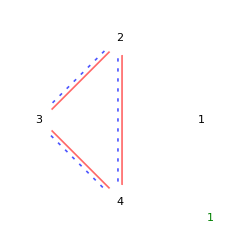
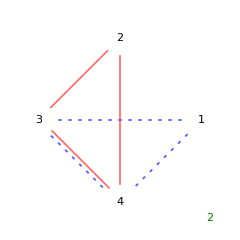
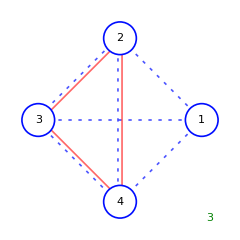
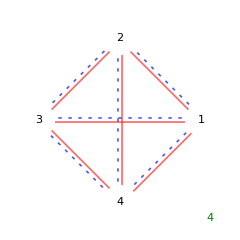
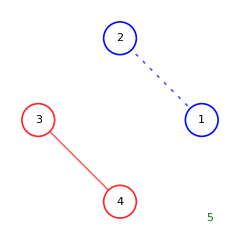
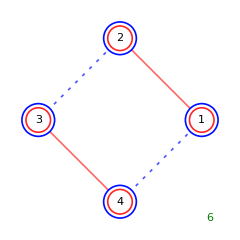

Number of possibilities: 6. Total computation time in seconds: 0.24992. Time used for Z-matrix sorting, finding possible companion W-matrices, match Z and W matrices to ZW-matrices, applying matrix rules, duplicate ZW-matrix eliminations, and graphing:{0.02324,-3.940918480149451×10^9+mxruletime,3.940918480216898×10^9-mxruletime,0.15921}

```mathematica
zwmatrices[4]
```